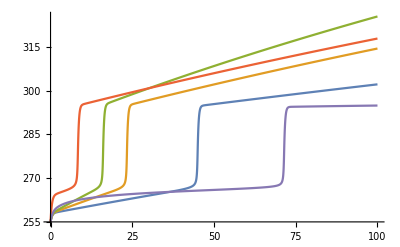

```mathematica
Clear[f,g,h];
ice=0.55;
water =0.3;
meltpoint=273.15;
variance = 10;
f[t_]:=If[t≤0,0,E^(-1/t)];
g[t_]:=f[t]/(f[t]+f[1-t]);
h[t_]:=(water-ice)*g[(t-(meltpoint-variance))/(2*variance)]+ice

S=1367;
α=0.55;
σ=5.670374419*10^(-8);
ϵ=0.612;
a=0.5;
b=0;
d1[t_,a_,b_] := a*t+b;
d2[t_]:=5*Log[t+1]
Clear[T,t]
s=NDSolve[{T'[t]==S/4(1-h[T[t]])-ϵ*σ*T[t]^4 +d1[t,0.5,0],T[0]==255},T,{t,0,100}];
u=NDSolve[{T'[t]==S/4(1-h[T[t]])-ϵ*σ*T[t]^4 +d1[t,1,0],T[0]==255},T,{t,0,100}];
v=NDSolve[{T'[t]==S/4(1-h[T[t]])-ϵ*σ*T[t]^4 +d1[t,1.5,0],T[0]==255},T,{t,0,100}];
w=NDSolve[{T'[t]==S/4(1-h[T[t]])-ϵ*σ*T[t]^4 +d1[t,1,15],T[0]==255},T,{t,0,100}];
x=NDSolve[{T'[t]==S/4(1-h[T[t]])-ϵ*σ*T[t]^4 +d2[t],T[0]==255},T,{t,0,500}];
Plot[{Evaluate[T[t]/.s],Evaluate[T[t]/.u],Evaluate[T[t]/.v],Evaluate[T[t]/.w],Evaluate[T[t]/.x]},{t,0,100},PlotRange->All]
```

```mathematica
T=(((1-α)S)/(4*ϵ*σ))^(1/4)
```

258.012